```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/float_sort_benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}];
```

```mathematica
data;
```

```mathematica
benchmarks={"bitonic_2n_float_key_value_sort_bench", "bitonic_8n_float_key_value_sort_bench","bitonic_float_key_value_sort_bench", "std_float_key_value_sort_bench"};
cols
```

{bitonic_2n_float_sort_bench/8,487365,1297.04,1289.54,ns,,,,,,8}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringPosition[data[[i,1]], name]=={{1,StringLength[name]}}  && Length[data[[i]]]>5),data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]];
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=SortBy[Transpose[{NumToSort3,timing3}], First];
p4=SortBy[Transpose[{NumToSort4,timing4}], First];
```

```mathematica
color=ColorData[10,"ColorList"];
benchmarks
LegendFontSize=20;
legenda=
PointLegend[{
{color[[1]],AbsolutePointSize[8]},
{color[[2]],AbsolutePointSize[8]},
{color[[3]],AbsolutePointSize[8]},
{color[[4]], AbsolutePointSize[8]},
Directive[color[[9]], AbsolutePointSize[8]]},
{Style["bitonic 2^n sort", LegendFontSize], Style["bitonic 8n sort", LegendFontSize], Style["bitonic arbitrary n sort", LegendFontSize], 
Style["std sort", LegendFontSize], Style["hybrid 8n sort", LegendFontSize],  Style["bitonic sort ver2", LegendFontSize]},
LegendLabel->"", LegendLayout->{"Row",6}];
```

{bitonic_2n_float_key_value_sort_bench,bitonic_8n_float_key_value_sort_bench,bitonic_float_key_value_sort_bench,std_float_key_value_sort_bench}

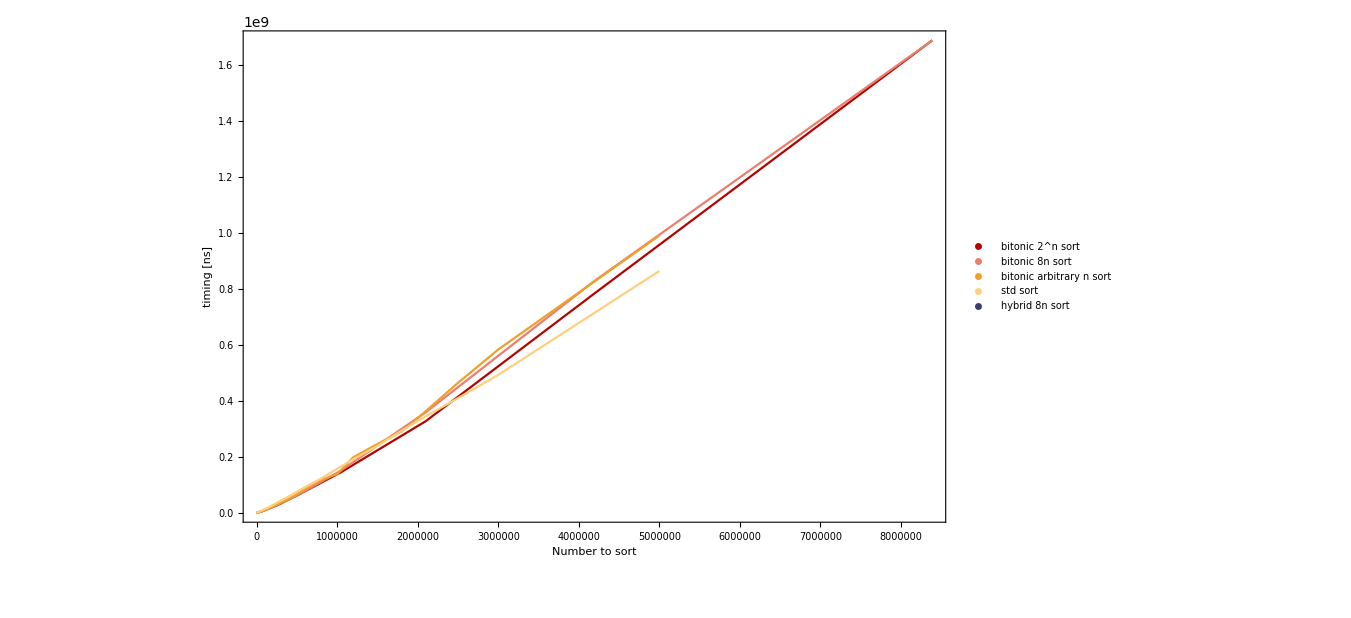

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {1*10^7, 4*10^9}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True, 
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->All,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

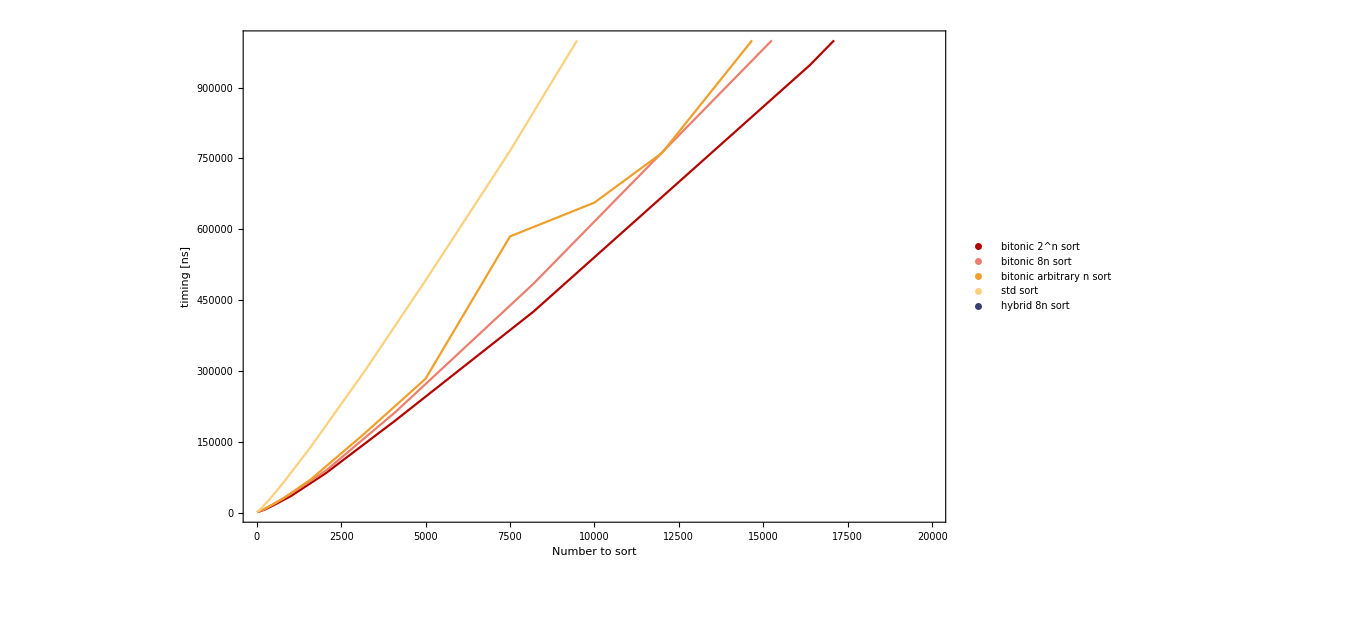

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {10^4, 2.2*10^5}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0, 20000},{0, 10 ^6}},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

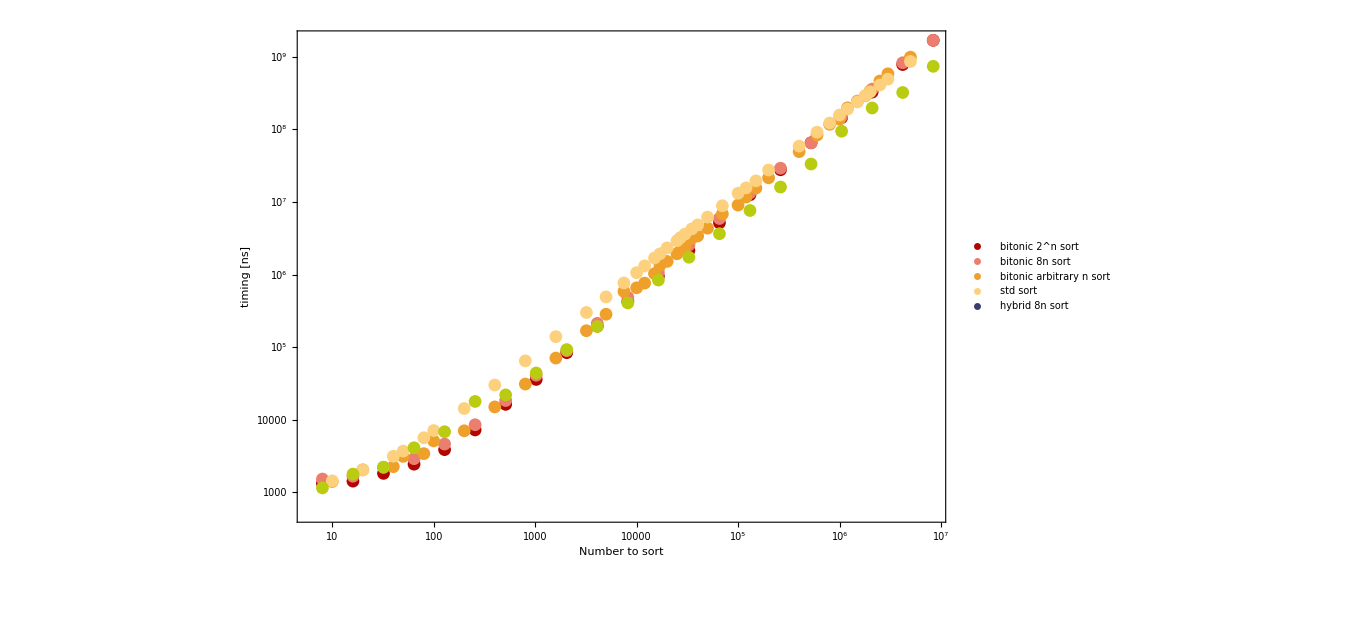

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLogLogPlot[{
p1,p2,p3,p4, p5
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-100, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

```mathematica
NonlinearModelFit[Take[p1, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p2, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p3, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p4, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[-21.1621 x-3.52746×10^-8 x^2+0.40404 x Log[x]^2]

FittedModel[32.4575 x+2.0947×10^-6 x^2+0.150832 x Log[x]^2]

FittedModel[52.1145 x+4.0741×10^-6 x^2+0.0578884 x Log[x]^2]

FittedModel[-3.51963 x-3.68749×10^-6 x^2+0.747879 x Log[x]^2]

```mathematica
(*speedup calculation in comparison to std*)

speedup1=Table[{p3[[i,1]],p4[[i,2]]/p3[[i,2]]},{i,1,p3//Length}]//N;
```

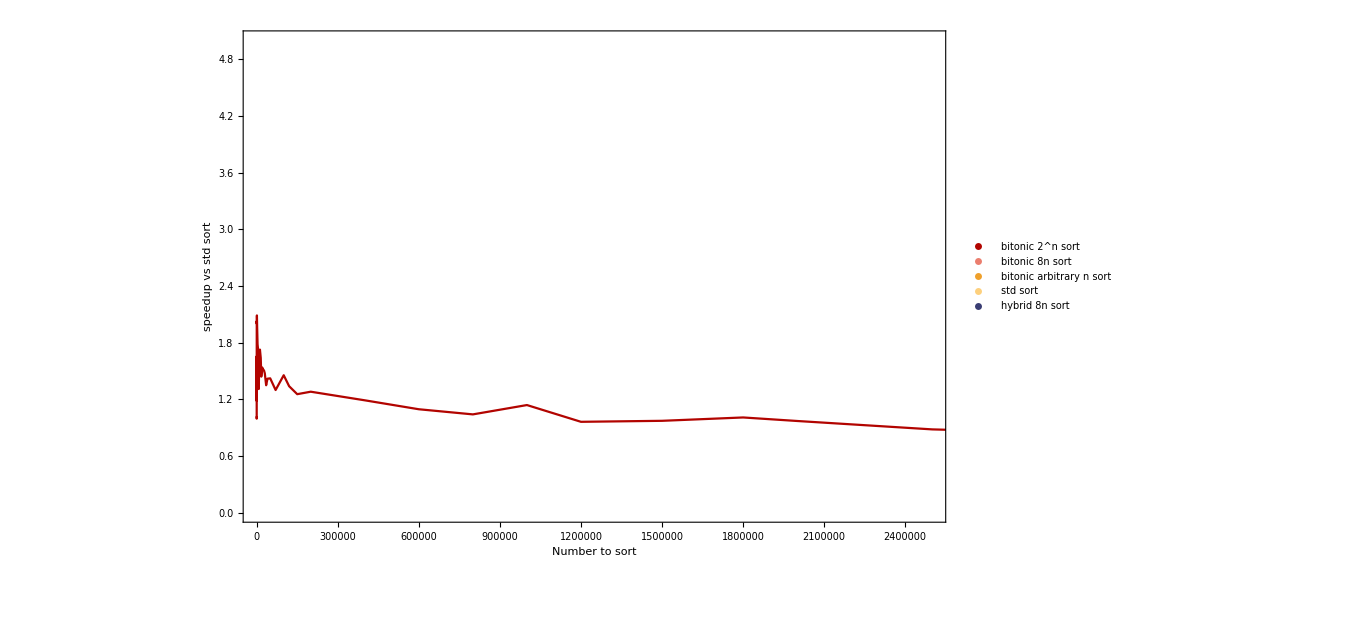

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{Automatic,{0,5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

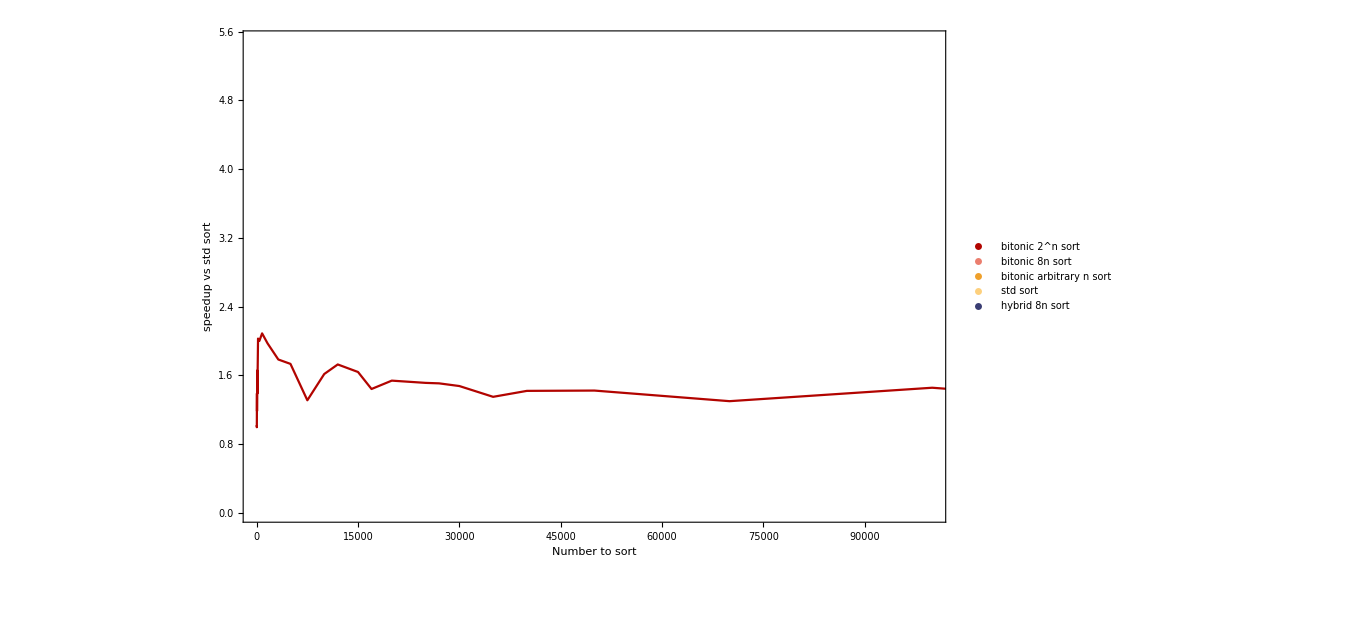

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0,100000},{0,5.5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```